# Nonequilibrium Green's function methods for thermal energy current, Version 6

Wang Jian-Sheng, 27 Dec 2007

References: 
(1) Linear case:  N. Mingo and L. Yang, PRB 68, 245406 (2003); A. Dhar and D. Sen, PRB 73, 085119 (2006); and P. A. Khomyakov, et al, PRB 72, 035450 (2005).
(2) Nonlinear, general derivation:  Y. Meir and N. S. Wingreen, PRL 68, 2512 (1992); A.-P. Jauho, N. S. Wingreen, and Y. Meir, PRB 50, 5528 (1994).
(3) General nonequilibrium Green's function methods:  L. Kadnoff and Baym's book,  J. Rammer and H. Smith, RMP 58, 323 (1986). 
See also J-S Wang, J Wang, and J-T Lu, quantum thermal transport in nanostructures, preprint.

The 1D spring model consists of spring constant k_1, k_2 for the left lead (site -∞, ..., -1, 0) and right lead (site Nmax+1, Nmax+2, ..., +∞).   The central part has k_c for the harmonic part connecting among sites 1, 2, ..., Nmax; and the interactions between the leads and central part are also k_1, k_2.  The central part has Nmax atoms. Masses of all particles are assumed the same, m.  (in program, k is already divided by the m, and t by m^(3/2)).    In addition, each of the lead atom has uniform on-site interaction with the substrate, k1onsite and k2onsite.  The nonlinear interation is the cubic-FPU model (α-model):
H_non= t ∑_(i=1)^(Nmax-1) (x_i-x_(i+1))^3 =1/3∑_(ijk=1)^Nmax T_ijk x_i x_j x_k
where for Nmax=2 T_111=3t, T_112=T_121=T_211=-3t, T_122=T_212=T_221=3t, and T_222=-3t.   The overall retarded Green's function G for the linear system is from [(ω+i η)^2-K]G=I.  η_→ 0^+.  Note that k and t in this program are actually rescaled by the mass of atoms through the transformation u_j→√m_j x_j.

In this version, a list of Green's functions is computed first. The list is generated if the function makeGlist[ ] is called. 

First, we set the model parameters numerically.  T_1 and T_2 are the temperatures of the left and right lead. We also set the infinitesimal small positive η here.  Units are such that /k_B=cof，and =cof2 in the current choice of units.   In such units, the mass m_0 is 1 amu. (atomic mass units, approximately mass of a proton,  1.66×10^-27kg ), original coupling k_0 is in units of 10^4 dyn/cm, and three-body coupling t_0 in eV/(Å m_0^(3/2))=2.368×10^51(SI units).     This implies that the units for time is T_0=1/ω_0=√(m_0/k_0)=1.288 ×10^-14sec,  units for  is 1/ (T_0^5 t^2).  Since we have fixed time T_0 and ,  the unit for energy must be E_0=/T_0=51.08 meV.  Unit for temperature is Kelvin.  The final thermal current can be converted to SI units by cof3 = ((ω)_0)^2=6.355×10^-7W = 635.5 nW (nano Watts).

We'll consider a 1D Carbon chain with parameters used in D Segal & A Nitzan, PRL 94, 034301 (2005).   Two body potential is V(x)=D ( exp(-α x)-1)^2， where D=3.8 eV, α=1.88 Å^-1.  mass = 12 amu.  This means for our program: k=2 Dα^2/m=2.24,  t=Dα^3/m^(3/2)=0.607  (sign not important).

```mathematica
Clear[order, k1,k1onsite,k2,k2onsite,kC, Nmax, w, T1, T2,t, η,cof, cof2,T,Tlist,i,j,k];

order = 0;
k1= 2.5;
k1onsite=0.0001;
k2=2.0;
k2onsite=0.0001;
kC=1.5;
Nmax=2;
T1= 295.0;
T2=305.0;
t=0.6;
η = 0.0001;
cof=592.467;
cof2 = 0.209985; 
cof3 = 635.5;

For[i=1,i≤Nmax,++i,
For[j=1,j≤Nmax,++j,
For[k=1,k≤Nmax,++k,
T[i,j,k]=0;
]
]
];
For[i=1,i<Nmax,++i,
j=i+1;
T[i,i,i]+=3t;
T[i,i,j]=T[i,j,i]=T[j,i,i]=-3t;
T[i,j,j]=T[j,i,j]=T[j,j,i]=3t;
T[j,j,j]+=-3t;
]
```

```mathematica
Tlist=Select[Flatten[Table[{i,j,k,T[i,j,k]}, {i,1,3},{j,1,3},{k,1,3}],2],(#[[4]]!=0)&]
```

{{1,1,1,1.8},{1,1,2,-1.8},{1,2,1,-1.8},{1,2,2,1.8},{2,1,1,-1.8},{2,1,2,1.8},{2,2,1,1.8},{2,2,2,-1.8}}

```mathematica
Export["D:\\temp\\Tlist.dat",Tlist,"Table"]
```

Order determine the terms of nonlinear self-energy: 0 linear system only (Σ_n=0), 1 to O(T^2),  2 to O(T^4).  We also clear all definitions and global variables

```mathematica
Clear[g,gl,fB,computeGr,makeGlist,wToi,Garray,getG,Σnf1,Σnf2,Σnf3,Σnf4,Σnf5,Σnf6,Σnf7,Σnf8,transmission,Glist,dwglobal,iMaxglobal,wMaxglobal]
```

## Green's functions for linear system

The definitions of various Green functions:
time ordered:		G_(j k)^T(t)=-i<T x_j(t) x_k(0)>,
anti-time ordered:  	G_(j k)^(T̄)(t)=-i<T̄ x_j(t) x_k(0)>,
retarded:  		G_(j k)^R(t)=-i θ(t)<[x_j(t), x_k(0)]>,
advanced: 		G_(j k)^A(t)=i θ(-t)<[x_j(t), x_k(0)]>,
less than:		G_(j k)^<(t)=-i<x_k(0) x_j(t)>,
greater than:		G_(j k)^>(t)=-i<x_j(t)x_k(0)>.
Note the general relations among the green functions.
Keldsh:		G^K=G^>+G^<=G^T+G^(T̄),
spectrum:		G̃=G^R-G^A=G^>-G^<,  and
			G^T=G^<+G^R,
			G^(T̄)=G^<-G^A.
In frequency domain, we also have  G^A[ω] = (G^R[ω])^†. These relations come from the definition of the Green's functions, thus are generally valid, whether it is in equilibrium or not.  In thermal equilibrium, we have additional relations which can be proved with Lehman represention:
G^<[ω] = e^-βω G^>[ω],  β=1/(k_B T), and G^<[ω]=f_B[ω](G^R[ω]-G^A[ω]),  f_B[ω]=1/(e^βω-1).   With these relations, only two Green's functions are independent in nonequilibrium case and one in equilibrium problem.  We also have symmetry relations in ω:  (G^(r,a)[ω])^*=G^(r,a)[-ω] (generally) and G_jj^<[-ω]=e^βω G_jj^<[ω] (in equilibrium).

g[ω,k,k'], k=k1 and k2, k' for onsite interaction, are the semi-infinite Green's functions (surface Green's functions for the free leads) at the conjunction, g_αα, or g_ββ.    x = exp(iq),  q is the wave number in dispersion relations (q can be complex).  x satisfies (ω+i η)^2-2k-k'+k x + k/x =0 .  g_L is the solution of the equation,  [(ω+iη)^2- K_L]g_L=I, which is -exp(i q)/k_1 in this simple model.  One should pay particularly the sign or branch choices such that g satisfies g[ω]=g^*[-ω] (The choose is such that Abs[exp(iq)]<1).  We need only the g_00 element.   We also need g^<, the less Green's functions of the leads.   We have set / k_B =cof.  We write out clearfully so that g^<[ω=0] is well-defined.  fB[ω,T] is Bose-Einstein distribution.

```mathematica
g[w_,k_,kp_]:=Module[{a},
If[w == 0,
-(2k+kp+η^2 - Sqrt[(kp+η^2)*(4k+kp+η^2)])/(2*k^2) ,
a=((w+I*η)^2-2k-kp)/(2k);
( a- Sign[w]*I*Sqrt[1-a^2])/k
]
];

gl[w_,k_,kp_,Tm_] :=Module[{x}, 
If[w==0,Limit[2*I*Im[g[x,k,kp]]/(Exp[cof*x/Tm]-1),x-> 0],
2*I*Im[g[w,k,kp]]/(Exp[cof*w/Tm]-1)]
];

fB[w_,Tm_]:=1/(Exp[cof*w/Tm]-1)
```

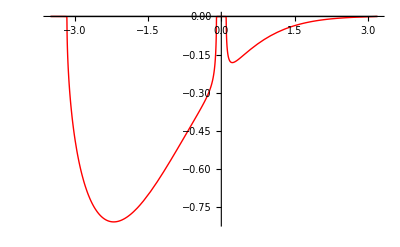

```mathematica
Plot[Evaluate[{Re[#],Im[#]}&[gl[w,k1,k1onsite,T1]]],{w,-3.5,3.2}, PlotStyle-> {RGBColor[0,0,0], RGBColor[1,0,0]}]
```

Construct the inverse A of central part Green function G^0 for linear system  (for simplicity, we omit the superscript 0, so Gr, Ga, Gl are for the linear system. Nonlinear, total green functions will be denoted Gnr, Gna, etc).  A G = I.  A = (ω+i η)^2-K_c-Σ_L-Σ_R,    Σ_L= V_(C L)g_L^r V_(L C) is called self-energy.    Note that there is only one nonzero element in the corner of V_(C L)=(V_(L C))^T.

```mathematica
computeGr[w_]:=Module[{A,i,j,Gr},
A=Table[Which[i==j,(w+I*η)^2-2*kC,
		Abs[i-j]==1, kC,
		True, 0],{i,1,Nmax},{j,1,Nmax}];A[[1,1]] += kC -k1-k1^2*g[w,k1,k1onsite];A[[Nmax,Nmax]] += kC -k2 -k2^2 *g[w,k2,k2onsite];Gr = Inverse[A];
Gr
]
```

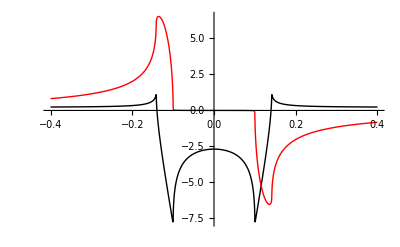

```mathematica
Plot[Evaluate[{Re[#],Im[#]}&[computeGr[w][[2,1]]]],{w,-0.4,0.4}, PlotStyle-> {RGBColor[0,0,0], RGBColor[1,0,0]}]
```

We give here other type of Green's functions, G^A= Hermitian conjugate of G^R, G^<= G^R Σ^<G^A.  This equation is true only because of the free leads.  Σ^<=Σ^(L<)+Σ^(R<), and Σ^(L<)=V^CL g^(L<)V^LC, similarly for the right lead.   We use G[σ,σ'] to denote G^σσ' where σ = ±1 (but 1 for + and 2 for - in program) , Note that G^(++)=G^T, G^(+-)=G^<, G^(-+)=G^>, G^(--)=G^(T̄).  The G^σσ'[ω] will be used in the integrand for the nonlinear self-energy.  MakeGlist[ ] generates a list of green functions stored in Glist. ωMax is the max range, nMax is number of points used. Glist and iMaxglobal etc are globals.

```mathematica
makeGlistSymmetrize[ωMax_, nMax_Integer]:= Module[{w,Gp,Gm},
dwglobal = 2.0*ωMax/(nMax-1);
Glist={};
For[w=-ωMax,w≤ωMax, w += dwglobal,
Gp = Garray[w];
Gm = Garray[-w];
Glist = Glist ~Join ~ {{{ (Gp[[1,1]]+Transpose[Gm[[1,1]]])/2,
(Gp[[1,2]]+Transpose[Gm[[2,1]]])/2},
{ (Gp[[2,1]]+Transpose[Gm[[1,2]]])/2,
(Gp[[2,2]]+Transpose[Gm[[2,2]]])/2}}};
];
iMaxglobal = Length[Glist];
wMaxglobal = ωMax;
]

wToi[ω_Real]:=Round[ 1.0 + (ω + wMaxglobal)*(iMaxglobal - 1)/(2.0*wMaxglobal)]

Garray[w_]:=Module[{Gr,Ga,Gl,Σl},
Gr=computeGr[w];
Ga=ConjugateTranspose[Gr];
Σl=Table[0,{Nmax},{Nmax}];
Σl[[1,1]]= k1^2*gl[w,k1,k1onsite,T1]; Σl[[Nmax,Nmax]]= k2^2*gl[w,k2,k2onsite,T2];
Gl =  Gr . Σl . Ga;
{{Gl+Gr, Gl},{Gr-Ga+Gl, Gl-Ga}}
]
```

General::spell1: Possible spelling error: new symbol name "Glist" is similar to existing symbol "Tlist". More…

General::spell1: Possible spelling error: new symbol name "wMaxglobal" is similar to existing symbol "iMaxglobal". More…

getG[i,s,sp,j,k] returns the value of green function G_jk^(σ σ')[ω] from the table Glist.  Note that index s varies from 1 to 2, 1 for σ=+, and 2 for σ= -.   However, we'll let σ and σp to run from 1 to 2 as well in the program. The mapping from frequency ω to index i is according to makeGlist[ ] defined in wToi[ ].  value outside the range -ωMax to +ωMax is set to zero (corresponding to index i from 1 to iMaxglobal).   There is one important symmetry property in G^σσ'[ω], that is
G_jk^σσ'[ω]=G_kj^σ'σ[-ω],  η → 0^+.
This is used because it makes the result more accurate.

```mathematica
getG[i_Integer, s_Integer,sp_Integer, j_Integer, k_Integer] := Module[{},
If[i ≤0 || i > iMaxglobal, Return [0.0]];
Glist[[i,s,sp,j,k]]
]
```

Generate table,  parameters can be changed.  Must re-run makeGlist after changing parameters.

```mathematica
makeGlistSymmetrize[20.5,1000];
```

```mathematica
ListPlot[Table[Re[getG[i,1,1,1,1]],{i,1,2000}],Joined->True,PlotRange->{-10,2}]
```

We now compute the self-energy Σ^σσ'[ω] due to the nonlinear contribution.  To lowest order, there are two graphs: a loop graph Σ1 and a balloon graph Σ2, which give the following formula: 
Σn_jk^σσ'[ω]=2i ∑_lmrs ∫_(-∞)^(+∞) T_jlm T_rsk Gn_lr^σσ'[ω']Gn_ms^σσ'[ω-ω']ⅆ ω'/(2π) + 2i σ δ_σσ'∑_lmrs ∑_σ'' σ''∫_(-∞)^(+∞) T_jkl T_mrs Gn_lm^σσ''[0]Gn_rs^σ''σ''[ω']ⅆ ω'/(2π).
The second term comes from the thermal expansion contribution.  It is independent of ω.   The Feynman diagram code for G (not Σ) is appended at the end of this program.  The formula (3-2s) maps 1 and 2 to +1, and -1, respectively (for σ'').   The second term is always real.

```mathematica
Σnf1[σ_Integer,σp_Integer, ω_Real]:=Module[{res,i,ip,i0,j,k,l,m,r,s,Y},
res = Table[0, {Nmax},{Nmax}];
i = wToi[ω];
i0=wToi[0.0];
If[t == 0, Return[res]];
For[l=1, l ≤ Nmax, ++l,
For[m=1,m≤ Nmax,++m,
For[r=1, r≤ Nmax, ++r,
For[s=1, s ≤ Nmax, ++s,
Y=dwglobal *Sum[getG[ip,σ,σp,l,r]*getG[i0+i-ip,σ,σp,m,s], {ip, 1, iMaxglobal}];
For[j=1, j≤ Nmax,++j,
For[k=1, k≤ Nmax, ++k,
res[[j,k]] += T[j,l,m]*T[r,s,k]*Y;
]
];
]
]
]
];
Return[cof2*res*I/Pi]
];

Σnf2[σ_Integer,σp_Integer, ω_Real]:=Module[{res,i0,ip,j,k,l,m,r,s,Y,σpp},
res = Table[0, {Nmax},{Nmax}];
If[t == 0, Return[res]];
If[σ ≠ σp, Return[res]];
i0=wToi[0.0];
For[r=1, r≤ Nmax, ++r,
For[s=1, s ≤ Nmax, ++s,
For[σpp=1,σpp≤2,++σpp,
Y=dwglobal *Sum[getG[ip,σpp,σpp,r,s], {ip, 1, iMaxglobal}] ;
Y = I*Im[Y];
For[l=1, l ≤ Nmax, ++l,
For[m=1,m≤ Nmax,++m,
For[j=1, j≤ Nmax,++j,
For[k=1, k≤ Nmax, ++k,
res[[j,k]] += (3-2*σp)*(3-2*σpp)*T[j,k,l]*T[m,r,s]*getG[i0,σ,σpp,l,m]*Y;
]
];
];
]
]
]
];
Return[Re[cof2*res*I/Pi]]
]
```

Rest of the O(T^4)  graphs nonlinear self-energy contribution, named in the order given in  PRB 74, 033408 (2006) paper.  The code below for third graph appears too slow to be useful, unless we got much powerful computer.  The naming according to the graphs in the paper Fig. 1.

```mathematica
Σnf3[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,n,o,r,s,t,u,v,w,σpp,σppp,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[n=1, n≤ Nmax, ++n,
For[o=1, o≤ Nmax, ++o,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[t=1, t≤ Nmax, ++t,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
Y=dwglobal^2 * Sum[getG[ipp,σ,σp,m,o]*getG[i0+i-ipp,σ,σpp,l,r] * getG[ip,σpp,σppp,s,v] * getG[2*i0+i-ip-ipp,σpp,σppp,t,w]*getG[i0+i-ipp,σppp,σp,u,n],{ip,1,iMaxglobal},{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,l,m]*T[n,o,k]*T[r,s,t]*T[v,u,w]*(3-2*σpp)*(3-2*σppp);
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-8.0)/(2.0*Pi)^2]
]
```

General::spell1: Possible spelling error: new symbol name "σppp" is similar to existing symbol "σpp". More…

```mathematica
Σnf4[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,r,s,u,v,w,x,y,z,σpp,σppp,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[x=1, x≤ Nmax, ++x,
For[y=1,y≤ Nmax, ++y,
For[z=1, z≤ Nmax, ++z,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
Y=dwglobal^2 * Sum[getG[ip,σ,σpp,l,u]*getG[i0+i-ip,σ,σppp,m,y] * getG[ipp,σppp,σpp,x,v] * getG[ip+ipp-i0,σpp,σp,w,r]*getG[2*i0+i-ip-ipp,σppp,σp,z,s],{ip,1,iMaxglobal},{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,l,m]*T[r,s,k]*T[u,v,w]*T[x,y,z]*(3-2*σpp)*(3-2*σppp);
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-8.0)/(2.0*Pi)^2]
]
```

```mathematica
Σnf5[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,r,s,u,v,w,x,y,z,σpp,σppp,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[x=1, x≤ Nmax, ++x,
For[y=1,y≤ Nmax, ++y,
For[z=1, z≤ Nmax, ++z,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
Y=dwglobal^2 * getG[i0,σpp,σppp,v,x]*Sum[getG[ip,σ,σpp,l,u]*getG[i0+i-ip,σ,σp,m,s] * getG[ip,σpp,σp,w,r] ,
{ip,1,iMaxglobal} ]* Sum[
 getG[ipp,σppp,σppp,y,z],{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,l,m]*T[r,s,k]*T[u,v,w]*T[x,y,z]*(3-2*σpp)*(3-2*σppp);
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-8.0)/(2.0*Pi)^2]
]
```

```mathematica
Σnf6[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,r,s,u,v,w,x,y,z,σpp,σppp,σ4,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
If[σ!=σp, Return[res]];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[x=1, x≤ Nmax, ++x,
For[y=1,y≤ Nmax, ++y,
For[z=1, z≤ Nmax, ++z,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
For[σ4=1, σ4≤2, ++σ4,
Y=dwglobal^2 * getG[i0,σ,σpp,l,m]*getG[i0,σppp,σ4,w,x] *Sum[getG[ip,σpp,σppp,r,u]*getG[ip,σppp,σpp,v,s], 
{ip,1,iMaxglobal} ]* Sum[
 getG[ipp,σ4,σ4,y,z],{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,k,l]*T[m,r,s]*T[u,v,w]*T[x,y,z]*(3-2*σ)*(3-2*σpp)*(3-2*σppp)*(3-2*σ4);
]
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-4.0)/(2.0*Pi)^2]
]
```

```mathematica
Σnf7[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,r,s,u,v,w,x,y,z,σpp,σppp,σ4,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
If[σ ≠σp, Return[res]];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[x=1, x≤ Nmax, ++x,
For[y=1,y≤ Nmax, ++y,
For[z=1, z≤ Nmax, ++z,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
For[σ4=1,σ4 ≤ 2, ++σ4,
Y=dwglobal^2 * getG[i0,σ,σpp,l,m]*Sum[getG[ip,σpp,σppp,r,u] * getG[ip,σ4,σpp,x,s] * getG[ipp,σppp,σ4,v,y]*getG[i0+ipp-ip,σ4,σppp,z,w],{ip,1,iMaxglobal},{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,k,l]*T[r,s,m]*T[u,v,w]*T[x,y,z]*(3-2*σ)*(3-2*σpp)*(3-2*σppp)*(3-2*σ4);
]
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-4.0)/(2.0*Pi)^2]
]
```

```mathematica
Σnf8[σ_Integer,σp_Integer, ω_Real]:=Module[{j,k,l,m,r,s,u,v,w,x,y,z,σpp,σppp,σ4,i0,i,ip,ipp,res,Y},
res = Table[0, {Nmax},{Nmax}];
If[σ!=σp, Return[res]];
i=wToi[ω];
i0=wToi[0.0];
For[l=1, l≤Nmax, ++l,
For[m=1, m≤ Nmax, ++m,
For[r=1, r ≤ Nmax, ++r,
For[s=1,s≤ Nmax, ++s,
For[u=1, u≤ Nmax, ++u,
For[v=1,v≤ Nmax, ++v,
For[w=1, w≤ Nmax, ++w,
For[x=1, x≤ Nmax, ++x,
For[y=1,y≤ Nmax, ++y,
For[z=1, z≤ Nmax, ++z,
For[σpp=1, σpp ≤2, ++σpp,
For[σppp=1, σppp≤2, ++σppp,
For[σ4=1, σ4≤2, ++σ4,
Y=dwglobal^2 * getG[i0,σ,σpp,l,m]*getG[i0,σpp,σppp,r,w] *getG[i0,σpp,σ4,s,x]*Sum[getG[ip,σppp,σppp,u,v], 
{ip,1,iMaxglobal} ]* Sum[
 getG[ipp,σ4,σ4,y,z],{ipp,1,iMaxglobal}];
For[j=1, j≤ Nmax, ++j,
For[k=1,k≤ Nmax, ++k,
res[[j,k]] += Y*T[j,k,l]*T[m,r,s]*T[u,v,w]*T[x,y,z]*(3-2*σ)*(3-2*σpp)*(3-2*σppp)*(3-2*σ4);
]
]
]
]
]
]
]
]
]
]
]
]
]
]
];
Return[cof2^2*res *(-2.0)/(2.0*Pi)^2]
]
```

Once the self-energy is computed, the Green's function Gn for the whole nonlinear system is obtained by solving the contour variable Dyson equation.  The results are (by applying the Langreth theorem and some algebra, see book by H Haug and A-P Jauho "Quantum Kinetics in Transport ... "), for Gn^R:  
Gn^R=G^R+G^R Σn^R Gn^R,
Gn^<=Gn^R Σn^<Gn^A+(1+Gn^R Σn^R)G^<(1+Σn^A Gn^A).
(See 5 Aug 05 note pages for a derivation).  Be careful about the difference between Gn and G.  We compute Gn in numerical form, as symbolic results are too slow.  (Gn^R[ω])^-1=A[ω] -Σn^R[ω].  Note that in the code T stands for time-ordered, ell for less <, r for retarded, and a for advanced, and the prefix n for numerical or nonlinear.  Finally, the current from the left lead is obtained from
<Q_L>=1/(2π)∫_(-∞)^(+∞) ωTr{Gn^R[ω]Σ_L^<[ω]+Gn^<[ω]Σ_L^A[ω]}ⅆω, Where Σ_L is the self-energy of the free lead (not the central part).  Σ_L^(<,A)={{k_1^2 g_L^(<,A), 0, ...},...,{0,...,0}}.  <Q_R> is similar. ( See 21 Sep 05, note page 30).   We take the symmetrized form (Q_L-Q_R)/2, which seems numerically more accurate. We can define an effective transmission by -2(Gn^R[ω]Σ_L^<[ω]+Gn^<[ω]Σ_L^A[ω])/[f_B(T_1)-f_B(T_2)]. ("-" because the integral give negative, 2 because in Landauer formula, we integrate from 0 to infinity.]  Note that the result is complex, the imaginary part is not very meaningful.  But the integral from -∞ to +∞ should be zero for Q for the imaginery part.  The transmission is calculated here by finite temperature difference.

```mathematica
transmission[w_]:=Module[ {i,j,one,nΣT,nΣl,nΣr,nΣa,A,Gr,Ga,Gl,Σl,nGr,nGa,nGl,nGlfirstterm,nGlsecondterm,QL,QR} ,
A=Table[Which[i==j,(w+I*η)^2-2*kC,
		Abs[i-j]==1, kC,
		True, 0],{i,1,Nmax},{j,1,Nmax}];A[[1,1]] += kC -k1-k1^2*g[w,k1,k1onsite];A[[Nmax,Nmax]] += kC -k2 -k2^2 *g[w,k2,k2onsite];Gr = Inverse[A];
Ga=ConjugateTranspose[Gr];
Σl=Table[0,{Nmax},{Nmax}];
Σl[[1,1]]= k1^2*gl[w,k1,k1onsite,T1]; Σl[[Nmax,Nmax]]= k2^2*gl[w,k2,k2onsite,T2];
Gl =  Gr . Σl . Ga;
If[order == 0,
nΣT = nΣl= Table[0,{Nmax},{Nmax}];
];
If[order > 0,
nΣT =Σnf1[1,1,w]+Σnf2[1,1,w];
nΣl=Σnf1[1,2,w];
];
If[order == 2,
nΣT+= Σnf3[1,1,w] + Σnf4[1,1,w]+Σnf5[1,1,w]+Σnf6[1,1,w]+Σnf7[1,1,w]+Σnf8[1,1,w];
nΣl += Σnf3[1,2,w]+Σnf4[1,2,w]+Σnf5[1,2,w];
];
nΣr=nΣT-nΣl;
nΣa = ConjugateTranspose[nΣr];
nGr=Inverse[A-nΣr];
nGa = ConjugateTranspose[nGr];
nGlfirstterm=nGr.nΣl.nGa;
one = IdentityMatrix[Nmax];
nGlsecondterm = (one + nGr.nΣr).Gl.(one + nΣa.nGa);
nGl = nGlfirstterm + nGlsecondterm;
QL =  k1^2*( nGr[[1,1]]*gl[w,k1,k1onsite,T1] + nGl[[1,1]]*Conjugate[g[w,k1, k1onsite]]  );
QR= k2^2*( nGr[[Nmax,Nmax]]*gl[w,k2,k2onsite,T2] + nGl[[Nmax,Nmax]]*Conjugate[g[w,k2, k2onsite]]  );
-(QL-QR)/(fB[w,T1]-fB[w,T2])
]
```

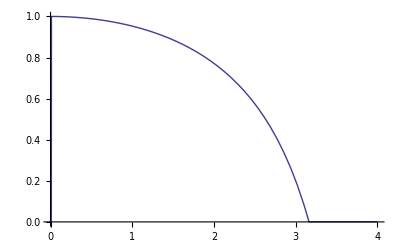

```mathematica
Plot[Re[transmission[w]],{w,0, 4.0}]
```

```mathematica
transdata = {};
For[w = 0.05, w ≤ 3.21, w += 0.05,
d = transmission[w];
Print["w=", w, "  d = ", d];
transdata = transdata ~Join~ { {w,d}}
]
```

The kappa[ ] compute the conductance, defined by κ = J/ΔT.  J is computed according to Landauer formua:  1/(2π)∫_0^∞  ω Trans[ω](f_L-f_R)ⅆω.  The imaginary part is supposedly 0.

```mathematica
kappa[tr_List]:=Module[{len,w,val,i},
len = Length[tr];
val = 0.0;
For[i = 1, i < len, ++i,
w = tr[[i,1]];
val += (tr[[i+1,1]]-w) * w* Re[tr[[i,2]]]*(fB[w,T1]-fB[w,T2]); 
];
cof3*val/(2.0*Pi)/(T1-T2)
]
```

Some checking that can be done: (1) If there is no nonlinearity, t=0, and k1=k2=kC, and T1=T2, k1onsite=k2onsite=0,  then the retarded green function is given exactly by G_jk=A e^(iq|j-k|), A=1/(2ik sin q),  We can write as G_jk=(-k g[ω])^(|j-k|)/(k^2(1/g[ω]-g[ω])).  Note that q can be complex when ω is in the gap.   

(2) for the same condition, we have two expressions for Gn^<:  Gn^<=Gn^R Σn^<Gn^A, (that is nGl), and  Gn^<=(Gn^R-Gn^A)f_B[ω]; they should be equal.

(3) If t=0, k and T1, T2 arbitrary, we can check against Caroli expression.  Mingo's equation for T is equivalent to Caroli expression T[ω]=Tr[ Γ_R G^r Γ_L G^a].   Notice that G=G^r=[G^a]^*.  Γ_L=i (Σ_L - Σ_L^*),  that is, the imaginary part of self-energy.  Only one element in Γ is nonzero for this model. 

(4) When t≠0, we don't have an effective method to check!

## Caroli or Mingo formula

```mathematica
Tmingo[w_]:=4*k1^2*k2^2*Im[g[w,k1,k1onsite]]*Im[g[w,k2,k2onsite]] *Conjugate[computeGr[w][[1,Nmax]]]*computeGr[w][[1,Nmax]];
```

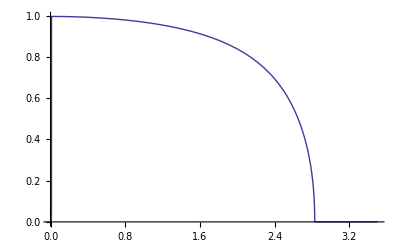

```mathematica
Plot[Tmingo[w], {w,0.00001,3.5}]
```

## Eigenvalues of transfer matrix method

Check the result of Zhang & Xiong, PRB 72 (2005) 115305.   They claim that the transmission from mode n  is given by  T_n=1/cosh^2 x_n,  where 2x_n is log eigenvalue of the transfer matrix M M^†.  The relevant theory is discussed in CWJ Beenakker, Rev Mod Phys 69 (1997) 731, section C1. It seems to me that the theory need to be modified when there is mode-mixing (that is t_nn' is not diagonal). General transfer matrix from coupling k to kp, site 0, 1 to 1, 2 (mass m=1) is P[w,kp,k].  Notice that the last argument k is on the left, kp on the right.    The transfP makes product of P according to the model.

```mathematica
Clear[w,P,p2mL,p2mR, nlead, transfP, M, m2eig,vRhalf, vLhalfinv,Tn, kL,kR,xL,xR];
P[w_,kp_,k_]:={{(-w^2+k+kp)/kp, -k/kp},{1,0}};
xL= 1-w^2/(2*k1)+I*Sqrt[w^2/k1-w^4/(4*k1^2)];
xR= 1-w^2/(2*k2)+I*Sqrt[w^2/k2-w^4/(4*k2^2)];
p2mL={{xL, 1/xL},{1,1}};
p2mR = {{xR, 1/xR}, {1,1}}
```

{{1-0.25 w^2+ⅈ √(0.5 w^2-0.0625 w^4),1/(1-0.25 w^2+ⅈ √(0.5 w^2-0.0625 w^4))},{1,1}}

Unlike the other two methods, which is exact, here we must consider lim_(n→∞) P_L^n P_c P_R^n, where P_L and P_R  are the transfer matrices for the left and right lead, and P_C is for the center part.  It turns out that limit is needed only in the frequency gap, and it converges very fast.    nlead is the number of n to use for the lead. 
The most critical part of this calculation is a transformation from the transform matrix P, defined by the displacement (u_(k+1),u_k)^T=P(u_1, u_0),  transformation M, defined by the amplitudes a^+, a^-.   See the Rev Mod Phys paper for detail.  For this problem, the transformation is,   Tau = inverse[p2mR] . P . p2mL.  Tau need further transformed by multiplying square roots of group velocities to get M. 

The program is not correct when two leads are different.  How to modified to make it work?

```mathematica
nlead = 6;
kL =k1;
kR=k2;
transfP[n_]:=Module[{mt},
mt={{1,0},{0,1}};
For[i=1, i<=n/2, ++i, 
mt = P[w,k1,k1].mt
];
mt = P[w,kC,kL].P[w,kL,k1].mt;
For[i=1,i<=Nmax-2,++i, 
mt=P[w,kC,kC].mt
];
mt=P[w,k2,kR].P[w,kR,kC].mt;
For[i=1, i<=n/2, ++i, 
mt = P[w,k2,k2].mt
];
mt];

vRhalf = {{Sqrt[k2*I*(1/xR-xR)]/(2*w),0}, {0,Sqrt[k2*I*(1/xR-xR)]/(2*w)}};
vLhalfinv = {{1/(Sqrt[k1*I*(1/xL-xL)]/(2*w)),0}, {0,1/(Sqrt[k1*I*(1/xL-xL)]/(2*w))}};

M[n_]= vRhalf.Inverse[p2mR].transfP[n].p2mL.vLhalfinv;
m2eig=Eigenvalues[M[nlead].ConjugateTranspose[M[nlead]]];
Tn[w_]=1/Cosh[0.5*Log[Abs[m2eig]]]^2;
```

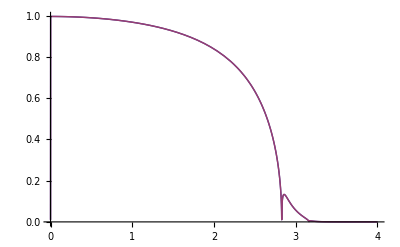

```mathematica
Plot[Evaluate[Tn[w]],{w,0,4.0}]
```

The little peak around 2.8 is an artifact of using finite nlead.   It should go to zero in the limit.

## Scattering boundary/mode-matching method

Now we use scattering boundary method to compute transitoin coefficient t and reflection coefficient r.  See J Wang and JS Wang, cond-mat/0509092.  The code works only for Nmax = 2.  Note we need the ratio of group velocity in T_sb.  v = -i k (e^iq-e^-iq)/(2ω).

```mathematica
Clear[sbEq,sbvec,r,t,w,S,Tsb];
sbEq={{-1,0,0,0,0,0,xL^2,0},
            {0,-1,0,0,0,0,xL,0},
            {-k1,-w^2+k1+kL,-kL, 0,0,0,0,0},
           {0,-kL, -w^2+kL+kC, -kC, 0, 0,0, 0},
           {0,0, -kC,-w^2+kC+kR, -kR, 0,0 , 0},
            {0,0,0,-kR,-w^2+kR+k2,-k2,0,0},
           {0,0, 0, 0, -1,0, 0, xR},
           {0,0,0,0,0,-1, 0, xR^2}};
sbvec={-1/xL^2, -1/xL, 0,0,0,0,0,0};
{r,t}=LinearSolve[sbEq, sbvec][[{7,8}]];
Tsb[w_] = Abs[t]^2 * Abs[k2 ( xR - 1/xR)/(k1(xL-1/xL))];
```

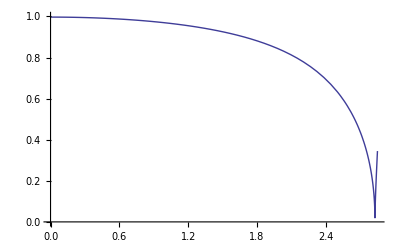

```mathematica
Plot[Tsb[w], {w, 0, 2.85}, PlotRange-> {0,1}]
```

Compute S-matrix.  S is unitary, S^†S=I.

```mathematica
S={{r,t},{t,r}};
```

## Feynman diagrammatic expansion for heat transport green functions with cubic nonlinear interactions

The coupling T[i,j,k] will be denoted by λ, which controls the order of expansion.  Maxorder is the highest order to compute, Grn[ {a,b,c},n] is green function with leg [a,b,c].  n indicates number λ generated so far in the final graph, used to generate dummy indices.  At the highest (top) level, we take n=0. Two terminating conditions for the grand recursion are first set.  Grn[] implements the resursion rules and also symmetrize with respect to the arguments with the orderless attributes.

```mathematica
Clear[maxorder,Grn,G,ts,permuterules];
maxorder = 4
```

4

```mathematica
SetAttributes[G, Orderless];
Grn[{},n_]:=-I;
Grn[arg_List, n_]:=0 /; n > maxorder
```

```mathematica
Grn[arg_List, n_Integer]:=Module[{len,k,j,newarg, res,tdummy},
len = Length[arg];
tdummy = ToExpression["t"<>ToString[n]];
res = 0;
For[k=1, k≤len, ++k,
newarg = Insert[ReplacePart[arg,tdummy,k],tdummy,k];
res += (1/len)*λ*G[arg[[k]],tdummy]*Grn[newarg,n+1];
For[j=1, j≤ len,++j,
If[j≠k,
res += (1/len) * I* G[arg[[k]],arg[[j]]]*Grn[Delete[arg,{{k},{j}}],n]; 
]; 
];
];
res // Simplify // Expand
]
```

```mathematica
g12=Grn[{1,2},0];
```

Canonize[] takes a term and puts into canonical form by permutating all dummy indices t_n and choices a particular one.

```mathematica
ts = Table[ ToExpression[ "t" <> ToString[k]],{k, 0, maxorder-1}];
permuterules = Map[Thread[ts -> #]&,Permutations[ts]];

canonize[fyn_]:= Module[{flist},
flist = Sort[fyn /. permuterules];
Return[flist[[1]]]
]
```

```mathematica
canonize /@ g12
```

G[1,2]+2 ⅈ λ^2 G[1,t1] G[2,t1] G[t0,t0] G[t0,t1]+2 ⅈ λ^2 G[1,t1] G[2,t0] G[t0,t1]^2+ⅈ λ^2 G[1,t1] G[2,t0] G[t0,t0] G[t1,t1]-4 λ^4 G[1,t3] G[2,t3] G[t0,t2]^2 G[t0,t3] G[t1,t1] G[t1,t2]-4 λ^4 G[1,t3] G[2,t2] G[t0,t2] G[t0,t3]^2 G[t1,t1] G[t1,t2]-4 λ^4 G[1,t2] G[2,t3] G[t0,t2] G[t0,t3]^2 G[t1,t1] G[t1,t2]-4 λ^4 G[1,t3] G[2,t3] G[t0,t1] G[t0,t2] G[t0,t3] G[t1,t2]^2-4 λ^4 G[1,t3] G[2,t2] G[t0,t1] G[t0,t3]^2 G[t1,t2]^2-8 λ^4 G[1,t3] G[2,t2] G[t0,t1] G[t0,t2] G[t0,t3] G[t1,t2] G[t1,t3]-8 λ^4 G[1,t3] G[2,t1] G[t0,t2]^2 G[t0,t3] G[t1,t2] G[t1,t3]-2 λ^4 G[1,t3] G[2,t3] G[t0,t1] G[t0,t2] G[t0,t3] G[t1,t1] G[t2,t2]-2 λ^4 G[1,t3] G[2,t2] G[t0,t1] G[t0,t3]^2 G[t1,t1] G[t2,t2]-2 λ^4 G[1,t2] G[2,t3] G[t0,t1] G[t0,t3]^2 G[t1,t1] G[t2,t2]-2 λ^4 G[1,t3] G[2,t2] G[t0,t1]^2 G[t0,t3] G[t1,t3] G[t2,t2]-2 λ^4 G[1,t2] G[2,t3] G[t0,t1]^2 G[t0,t3] G[t1,t3] G[t2,t2]-8 λ^4 G[1,t3] G[2,t1] G[t0,t1] G[t0,t2] G[t0,t3] G[t1,t3] G[t2,t2]-λ^4 G[1,t3] G[2,t2] G[t0,t0] G[t0,t3] G[t1,t1] G[t1,t3] G[t2,t2]-λ^4 G[1,t2] G[2,t3] G[t0,t0] G[t0,t3] G[t1,t1] G[t1,t3] G[t2,t2]-4 λ^4 G[1,t3] G[2,t0] G[t0,t2] G[t0,t3] G[t1,t1] G[t1,t3] G[t2,t2]

Draw Feynman diagrams from above results:  (1) draw n vertices if there is a λ^n,  label the vertices as t_0, t_1, ..., t_(n-1), plus two extra terminals 1 and 2, connect with lines if there is a green function G[a,b].   G[a,b] is the green function without the cubic interaction, still nonequilibrum (contour ordered) green functions.  The numerical factors are the same as in the above formula.  Finally, the dummy indices t_k=(j,t) have to be summed (for lattice site indices) and integrated (for time on the contour).